```mathematica
Sin[1.3]
```

0.963558

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
ag1 = 3 - 5 * t
```

3-5 t

```mathematica
t = 3
```

3

```mathematica
ag1
```

-12

```mathematica
Clear[t]
```

```mathematica
ag1 /. t -> 3.
```

-12.

```mathematica
ag1
```

3-5 t

```mathematica
myfun[t_] := 3.5*t^2-4.*t+7.
```

```mathematica
myfun[3.]
```

26.5

```mathematica
D[myfun[x],x]
```

-4.+7. x

```mathematica
myfun[a_,b_,c_,t_] := a*t^2+b*t+c
```

```mathematica
myfun[1.,2.,3.,4.]
```

27.

```mathematica
myfun[3.]
```

26.5

```mathematica
myfun[1.,2.]
```

myfun[1.,2.]

```mathematica
?myfun
```

Global`myfun

myfun[t_]:=3.5 t^2-4. t+7.
 
myfun[a_,b_,c_,t_]:=a t^2+b t+c

```mathematica
fun1 = Function[{x},3*x^2]
```

Function[{x},3 x^2]

```mathematica
fun1[1.64]
```

8.0688

```mathematica
fun1[1.64,2,3]
```

8.0688

```mathematica
D[fun1[x],x]
```

6 x

```mathematica
fun2 = 3. * #1^2 &
```

3. #1^2&

```mathematica
fun2[1.6]
```

7.68

```mathematica
fun1c = Compile[{x},3*x^2]
```

CompiledFunction[…]

```mathematica
fun1c[1.6]
```

7.68

```mathematica
fun1c[x]
```

CompiledFunction::cfsa: Argument x at position 1 should be a machine-size real number.

3 x^2

```mathematica
mat = {{a,b,c},{d,e,f}}
```

{{a,b,c},{d,e,f}}

```mathematica
funq[x_] := x^2
```

```mathematica
Map[funq,mat,{2}]
```

{{a^2,b^2,c^2},{d^2,e^2,f^2}}

```mathematica
fun10[x_] := {x[[1]],x[[2]]^2,Sqrt[x[[3]]]}
```

```mathematica
MatrixForm[Map[fun10,mat]]
```

(a | b^2 | √c
d | e^2 | √f)

```mathematica
fun11[x_,y_,z_] := {x,y^2,Sqrt[z]}
```

```mathematica
MatrixForm[Apply[fun11,mat,{1}]]
```

(a | b^2 | √c
d | e^2 | √f)

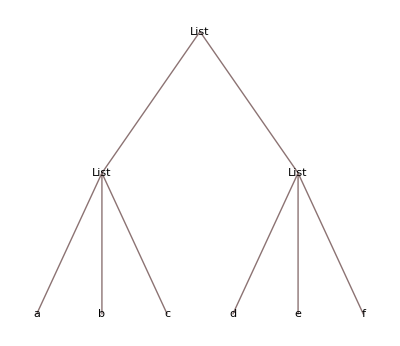

```mathematica
TreeForm[mat]
```

```mathematica
SetDirectory["\\\\nb-u\\utz\\math_kurs\\data"]
```

\\nb-u\utz\math_kurs\data

```mathematica
Directory[]
```

\\nb-u\utz\math_kurs\data

```mathematica
FileNames["*.dat"]
```

{echo89.dat,pardat2.dat,Rdat2.dat,Rdat3.dat,Rdat4.dat,Statistk1.dat}

```mathematica
data = Import["Rdat3.dat","Table"];
```

```mathematica
Length[data]
```

31

```mathematica
Dimensions[data]
```

{31,2}

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points {1,y_1},{2,y_2},…. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{data_1,data_2,…}] plots data from all the data_i.
ListPlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.

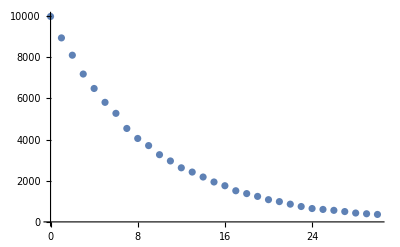

```mathematica
ListPlot[data]
```

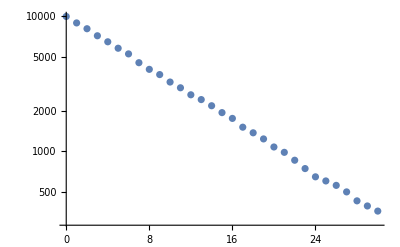

```mathematica
ListLogPlot[data]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
?ErrorListPlot
```

ErrorListPlot[{{y_1,dy_1},{y_2,dy_2},…}] plots points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] plots points with specified x and y coordinates and error magnitudes.

```mathematica
funerr[x_,y_] := {{x,N[y]},ErrorBar[Sqrt[N[y]]]}
```

```mathematica
Apply[funerr,data[[1;;5]],{1}]
```

{{{0.,9975.},ErrorBar[99.8749]},{{1.,8934.},ErrorBar[94.5198]},{{2.,8094.},ErrorBar[89.9667]},{{3.,7179.},ErrorBar[84.729]},{{4.,6478.},ErrorBar[80.486]}}

```mathematica
ErrorListPlot[Apply[funerr,data,{1}]]
```

-Graphics-

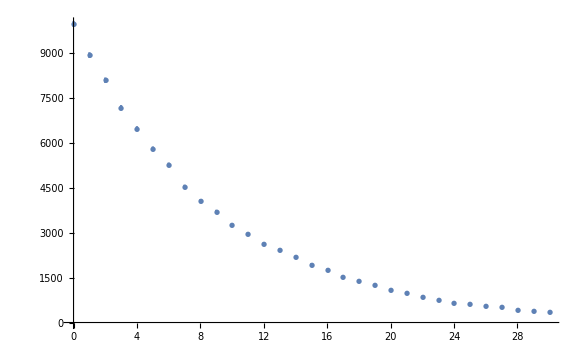

```mathematica
ErrorListPlot[Apply[funerr,data,{1}],PlotMarkers-> {Automatic,7}]
```